# Data visualisation 4 - Customising the look

## Customising the appearance of charts

We have thus far not cared much about how our plots look, other than making sure they are readable. However, we will soon delve into explanatory data visualisation, so we need to know how to control the appearance of all elements of a plot.

We will learn this by seeing all the steps taken in transforming a plot generated using Mathematica’s defaults into a much better, highly customised plot. The initial plot is this line plot, showing two time series:

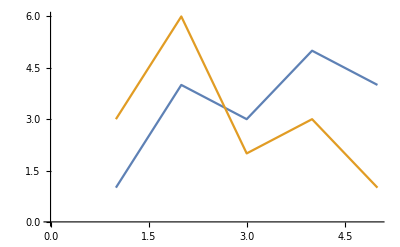

```mathematica
ListPlot[{{1,4,3,5,4},{3,6,2,3,1}},Joined->True]
```

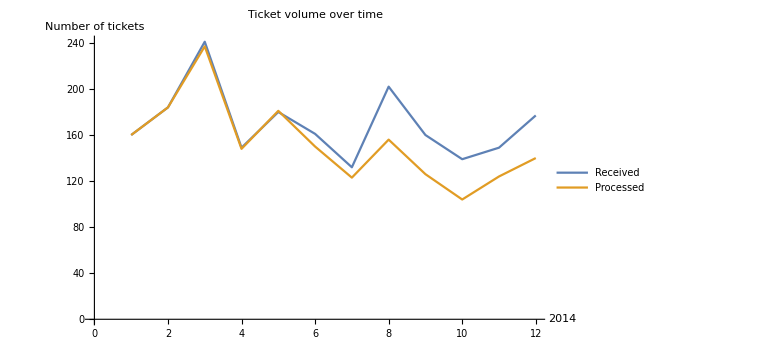

```mathematica
ticketsRec = {160,184,241,149,180,161,132,202,160,139,149,177};
ticketsProc= {160,184,237,148,181,150,123,156,126,104,124,140};

ListPlot[{ticketsRec, ticketsProc},
	Joined->True,
	PlotLabel->"Ticket volume over time",
	AxesLabel->{2014, "Number of tickets"},
	PlotLegends->{"Received", "Processed"},
	ImageSize->Large
]
```

We want to convert this plot into this one:

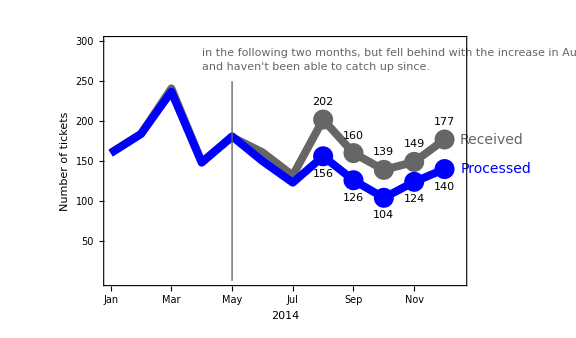

This is an example taken from the book Storytelling with Data, which I highly recommend. We won’t discuss here why this plot looks the way it does - this example will be discussed thoroughly when we talk about the principles and applications of explanatory data visualisation. Right now, we just want to know how to convince Mathematica to make the plot look like this.

### Customising the axes

First let us customise the axes. We want the axes to display the month abbreviations - that is, Jan, Feb, etc - rather than numbers. We also want to extend both axes a little beyond the default range. In addition, we want to plot fewer marks on the vertical axes. Here is how to achieve this:

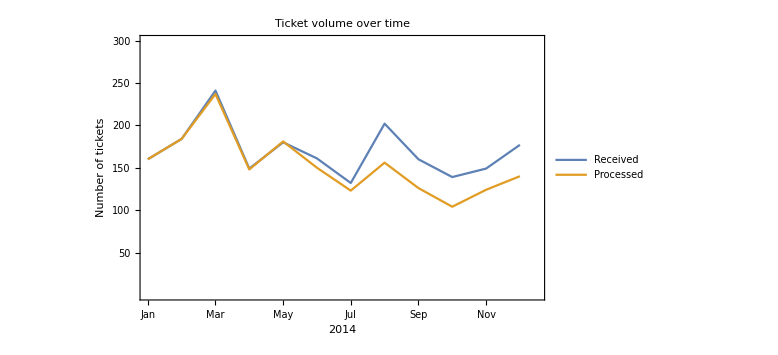

```mathematica
ticketsRec = {160,184,241,149,180,161,132,202,160,139,149,177};
ticketsProc= {160,184,237,148,181,150,123,156,126,104,124,140};
ticketDates = {"Jan", "Feb", "Mar", "Apr", "May", "Jun", "Jul",
			   "Aug", "Sep", "Oct", "Nov", "Dec"};

ListPlot[{ticketsRec, ticketsProc},
	Joined->True,
	PlotLabel->"Ticket volume over time",
	PlotLegends->{"Received", "Processed"},

	Frame->{True, True, False, False},
	FrameLabel->{"2014", "Number of tickets"},
	LabelStyle->{13,13},
	PlotRange->{{1,12.5}, {0,300}},
	FrameTicks->{Transpose[{Range[12],ticketDates}],
	            Range[50,300,50]},
	FrameTicksStyle->{12, 12},
		
	ImageSize->Large
]
```

```mathematica
Range[50,300,50]
```

{50,100,150,200,250,300}

The added or changed code is highlighted in orange. In order to do better customise the way the axes look, we need to switch from axes to frames, which are a more flexible version of axes. Frames allow you to define axes on all four sides of the plot, and they allow more control over how they are drawn. The commands

Frame→{True, True, False, False},
	FrameLabel→{“2014”, “Number of tickets”},
	LabelStyle→{13,13},
	PlotRange→{{1,12.5}, {0,300}},

define a frame with axes on the left and on the bottom of the plot, set their labels, and set their style - the way they should be drawn. In this case, we set the font sizes of both horizontal and vertical labels to 13. We also set the range of the horizontal and vertical axes, respectively.

FrameTicks→{Transpose[{Range[12],ticketDates}],
	                             Range[50,300,50]},

The FrameTicks command allows us to determine exactly where each tick (axes mark) will be drawn, and how it should be labeled. This is where we tell the horizontal axis to draw the month names, and we tell the vertical axis to draw ticks with larger spacing. To understand how it works, let us be totally explicit and write out the result of the Transpose and Range functions:

FrameTicks→{ {{1, “Jan”}, {2, “Feb”}, {3, “Mar”}, 
                                   {4, “Apr”}, {5, “May”}, {6, “Jun”}, 
                                   {7, “Jul”}, {8, “Aug”}, {9, “Sep”}, 
                                   {10, “Oct”}, {11, “Nov”}, {12, “Dec”}},
                                   
	                         {50,100,150,200,250,300} }

The first list is a list of pairs of numbers and names of months, and it determines the horizontal ticks. The numbers are the position on the axis, and the second member of the pair is what should be printed at that position. So this is instructing Mathematica to print Jan at position 1 of the horizontal axis, Feb at position 2, etc.

The second list refers to the vertical axis, and it is just a list of numbers, rather than pairs. This means that Mathematica will print at those positions in the default way - in this case, it will simply print the numbers at those positions.

If instead of a list of pairs we have a list of triples, the third element sets the size of the tick mark. So for example, if we had

FrameTicks→{ {{1, “Jan”,0}, {2, “Feb”,0}, {3, “Mar”,0}, 
                                   {4, “Apr”,0}, {5, “May”,0}, {6, “Jun”,0}, 
                                   {7, “Jul”,0}, {8, “Aug”,0}, {9, “Sep”,0}, 
                                   {10, “Oct”,0}, {11, “Nov”,0}, {12, “Dec”,0}},
                                   
	                         {50,100,150,200,250,300} }

then the tick marks are all set to zero, and they would not be present. This is what we want to do for the horizontal axis. This can be achieved by the more compact notation:

FrameTicks→{Map[{#⟦1⟧, #⟦2⟧, 0}&, Transpose[{Range[12], ticketDates}]],
	                             Range[50, 300, 50]},

Finally, the FrameTicksStyle[{12,12}] sets the font size of the tick labels to 12.

### Controlling the way data is displayed

We want to change the colours of the two lines to blue and gray, and make them thicker. We also want to display the points for August and later. This is how we do it:

```mathematica
ptsRec
```

{{1,160},{2,184},{3,241},{4,149},{5,180},{6,161},{7,132},{8,202},{9,160},{10,139},{11,149},{12,177}}

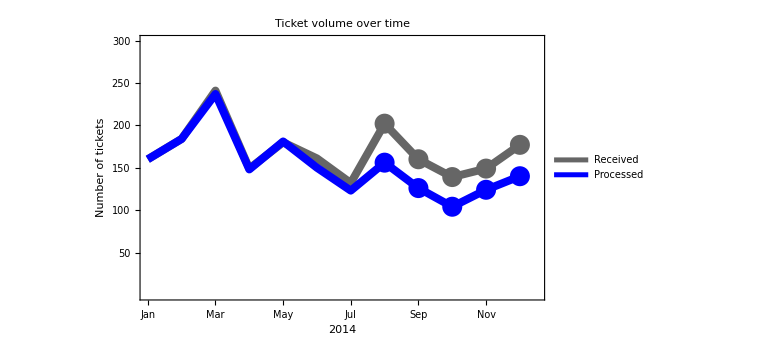

```mathematica
ticketsRec = {160,184,241,149,180,161,132,202,160,139,149,177};
ticketsProc= {160,184,237,148,181,150,123,156,126,104,124,140};
ticketDates = {"Jan", "Feb", "Mar", "Apr", "May", "Jun", "Jul",
			   "Aug", "Sep", "Oct", "Nov", "Dec"};
ptsRec = Transpose[{Range[12], ticketsRec}];
ptsProc = Transpose[{Range[12], ticketsProc}];

ptsRecAfter = Select[ptsRec, #⟦1⟧ > 7&];
ptsProcAfter = Select[ptsProc, #⟦1⟧ > 7&];

ListPlot[{ptsRec, ptsProc, ptsRecAfter, ptsProcAfter},
	Joined->{True, True, False, False},
	PlotStyle->{
        Directive[GrayLevel[0.4],Thickness[0.01]],
        Directive[Blue,Thickness[0.01]],
        Directive[GrayLevel[0.4],PointSize[0.025]],
        Directive[Blue,PointSize[0.025]]
    },
	PlotLabel->"Ticket volume over time",
	AxesLabel->{2014, "Number of tickets"},
	PlotLegends->{"Received", "Processed"},

	Frame->{True, True, False, False},
	FrameLabel->{"2014", "Number of tickets"},
	LabelStyle->{13,13},
	PlotRange->{{1,12.5}, {0,300}},
	FrameTicks->{Map[{#⟦1⟧,#⟦2⟧,0}&, Transpose[{Range[12],ticketDates}]],
	            Range[50,300,50]},
	FrameTicksStyle->{12, 12},
	ImageSize->Large
]
```

Let us see what this new code does:

ptsRec = Transpose[{Range[12], ticketsRec}];
	ptsProc = Transpose[{Range[12], ticketsProc}];

This results in pairs of month numbers and tickets. So, for example, ptcRec is {{1,160}, {2,184}, ...}.

ptsRecAfter = Select[ptsRec, #⟦1⟧ > 7&];
	ptsProcAfter = Select[ptsProc, #⟦1⟧ > 7&];

This creates lists of points for August (month 8) and later. The idea is that we will plot lines for all data points (with the Joined option set to True), and then plot points only for the points dated August or later (with the Joined option set to false). When we are plotting multiple data sets in ListPlot, we can set Joined individually for each set, by passing it a list, as is done in the code:

ListPlot[{ptsRec, ptsProc, ptsRecAfter, ptsProcAfter},
		       Joined→{True, True, False, False},

Now we need to set the colour, thickness (for the lines) and point size (for the points). This is done in the next few lines:

PlotStyle→{
        Directive[GrayLevel[0.4],Thickness[0.01]],
        Directive[Blue,Thickness[0.01]],
        Directive[GrayLevel[0.4],PointSize[0.025]],
        Directive[Blue,PointSize[0.025]]
    },

The appearance of each of the data sets is set by the four elements of the list passed to PlotStyle. Each entry in the list is a graphics directive, like the ones we encountered before when discussing graphics primitives. If we need to set more than one directive, we list them using the Directive command.

### Labeling points, and understanding Style

We will write the number of tickets above and below the points in August and later, as shown in the target figure. We want them to have the same colour as the lines and points of the corresponding plots, and we want to be able to set their font size. Our strategy is to create lists of Text objects, and use the Epilog option to display them on the graph. If we didn’t care about how the text is formatted, we could write something like this:

```mathematica
labelsRec = Map[Text[#⟦2⟧, #+{0,22}]&,
                ptsRecAfter]
```

{Text[202,{8,224}],Text[160,{9,182}],Text[139,{10,161}],Text[149,{11,171}],Text[177,{12,199}]}

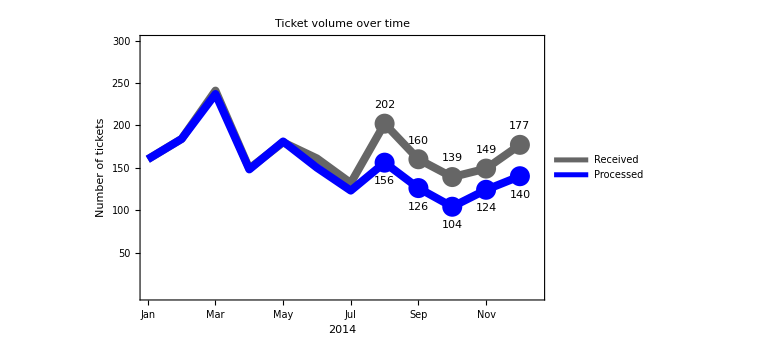

```mathematica
ticketsRec = {160,184,241,149,180,161,132,202,160,139,149,177};
ticketsProc= {160,184,237,148,181,150,123,156,126,104,124,140};
ticketDates = {"Jan", "Feb", "Mar", "Apr", "May", "Jun", "Jul",
			   "Aug", "Sep", "Oct", "Nov", "Dec"};
ptsRec = Transpose[{Range[12], ticketsRec}];
ptsProc = Transpose[{Range[12], ticketsProc}];

ptsRecAfter = Select[ptsRec, #⟦1⟧ > 7&];
ptsProcAfter = Select[ptsProc, #⟦1⟧ > 7&];
labelsRec = Map[Text[#⟦2⟧, #+{0,22}]&,
                ptsRecAfter];
labelsProc = Map[Text[#⟦2⟧, #-{0,22}]&,
                 ptsProcAfter];

ListPlot[{ptsRec, ptsProc, ptsRecAfter, ptsProcAfter},
	Joined->{True, True, False, False},
	PlotStyle->{
        Directive[GrayLevel[0.4],Thickness[0.01]],
        Directive[Blue,Thickness[0.01]],
        Directive[GrayLevel[0.4],PointSize[0.025]],
        Directive[Blue,PointSize[0.025]]
    },	
    PlotLabel->"Ticket volume over time",
	AxesLabel->{2014, "Number of tickets"},
	PlotLegends->{"Received", "Processed"},

	Frame->{True, True, False, False},
	FrameLabel->{"2014", "Number of tickets"},
	LabelStyle->{13,13},
	PlotRange->{{1,12.5}, {0,300}},
	FrameTicks->{Map[{#⟦1⟧,#⟦2⟧,0}&, Transpose[{Range[12],ticketDates}]],
	            Range[50,300,50]},
	FrameTicksStyle->{12, 12},
	ImageSize->Large,
	
	Epilog->{
		labelsRec, labelsProc
	}
]
```

The lines

labelsRec = Map[Text[#⟦2⟧, #+{0,22}]&,
          	      			    ptsRecAfter];

create a list of Text objects displaying the number of tickets (the second coordinate of the points), placed at the same horizontal coordinate of the plotted points, but at a height 22 greater; so they will be plotted above each point.

However, we do care about how the numbers look. So we customise their appearance by using the Style command. Style can be used to customise the appearance of anything that is displayed by Mathematica. For example:

```mathematica
{1, Style[2,Bold], Style[3, Blue], Style[4, FontSize->24], Style[5, Gray, Bold, Italic]}
```

{1,2,3,4,5}

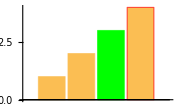

```mathematica
tstData = {1, 2, Style[3, Green], Style[4, EdgeForm[{Thick,Red}]]};
BarChart[tstData, ImageSize->Small]
```

Styles applied to points override styles defined in plotting options. In the above bar chart, for example, the default style of the bars is yellow with a thin black outline. But the third bar is green, and the outline of the second bar is thick and red, because those styles were set directly in the data.

We can now set the look of the labels of our points:

```mathematica
labelsRec = Map[Style[Text[#⟦2⟧, #+{0,22}], 
                      FontColor->Blue, FontSize->13]&,
                ptsProcAfter]//InputForm
```

{Style[Text[156, {8, 178}], FontColor -> 
   RGBColor[0, 0, 1], FontSize -> 13], 
 Style[Text[126, {9, 148}], FontColor -> 
   RGBColor[0, 0, 1], FontSize -> 13], 
 Style[Text[104, {10, 126}], FontColor -> 
   RGBColor[0, 0, 1], FontSize -> 13], 
 Style[Text[124, {11, 146}], FontColor -> 
   RGBColor[0, 0, 1], FontSize -> 13], 
 Style[Text[140, {12, 162}], FontColor -> 
   RGBColor[0, 0, 1], FontSize -> 13]}

```mathematica
ticketsRec = {160,184,241,149,180,161,132,202,160,139,149,177};
ticketsProc= {160,184,237,148,181,150,123,156,126,104,124,140};
ticketDates = {"Jan", "Feb", "Mar", "Apr", "May", "Jun", "Jul",
			   "Aug", "Sep", "Oct", "Nov", "Dec"};
ptsRec = Transpose[{Range[12], ticketsRec}];
ptsProc = Transpose[{Range[12], ticketsProc}];

ptsRecAfter = Select[ptsRec, #⟦1⟧ > 7&];
ptsProcAfter = Select[ptsProc, #⟦1⟧ > 7&];
labelsRec = Map[Style[Text[#⟦2⟧, #+{0,22}], 
                      FontColor->Gray, FontSize->13]&,
                ptsRecAfter];
labelsProc = Map[Style[Text[#⟦2⟧, #-{0,22}], 
                       FontColor->Blue, FontSize->13]&,
                 ptsProcAfter];

ListPlot[{ptsRec, ptsProc, ptsRecAfter, ptsProcAfter},
	Joined->{True, True, False, False},
	PlotStyle->{
        Directive[GrayLevel[0.4],Thickness[0.01]],
        Directive[Blue,Thickness[0.01]],
        Directive[GrayLevel[0.4],PointSize[0.025]],
        Directive[Blue,PointSize[0.025]]
    },	
	PlotLabel->"Ticket volume over time",
	AxesLabel->{2014, "Number of tickets"},
	PlotLegends->{"Received", "Processed"},

	Frame->{True, True, False, False},
	FrameLabel->{"2014", "Number of tickets"},
	LabelStyle->{13,13},
	PlotRange->{{1,12.5}, {0,300}},
	FrameTicks->{Map[{#⟦1⟧,#⟦2⟧,0}&, Transpose[{Range[12],ticketDates}]],
	            Range[50,300,50]},
	FrameTicksStyle->{12, 12},
	ImageSize->Large,
	
	Epilog->{
		labelsRec, labelsProc
	}
]
```

-Graphics-

### Labeling each line

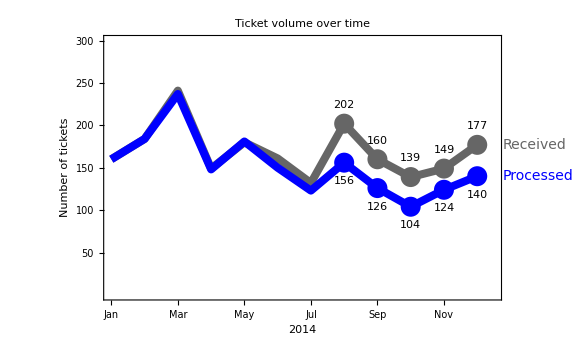

```mathematica
ticketsRec = {160,184,241,149,180,161,132,202,160,139,149,177};
ticketsProc= {160,184,237,148,181,150,123,156,126,104,124,140};
ticketDates = {"Jan", "Feb", "Mar", "Apr", "May", "Jun", "Jul",
			   "Aug", "Sep", "Oct", "Nov", "Dec"};
ptsRec = Transpose[{Range[12], ticketsRec}];
ptsProc = Transpose[{Range[12], ticketsProc}];

ptsRecAfter = Select[ptsRec, #⟦1⟧ > 7&];
ptsProcAfter = Select[ptsProc, #⟦1⟧ > 7&];
labelsRec = Map[Style[Text[#⟦2⟧, #+{0,22}], 
                      FontColor->Gray, FontSize->13]&,
                ptsRecAfter];
labelsProc = Map[Style[Text[#⟦2⟧, #-{0,22}], 
                       FontColor->Blue, FontSize->13]&,
                 ptsProcAfter];

ListPlot[{ptsRec, ptsProc, ptsRecAfter, ptsProcAfter},
	Joined->{True, True, False, False},
	PlotStyle->{
        Directive[GrayLevel[0.4],Thickness[0.01]],
        Directive[Blue,Thickness[0.01]],
        Directive[GrayLevel[0.4],PointSize[0.025]],
        Directive[Blue,PointSize[0.025]]
    },	
	PlotLabel->"Ticket volume over time",
	AxesLabel->{2014, "Number of tickets"},
	PlotLabels->Placed[{None, None, 
	                    Style["Received", GrayLevel[0.4], FontSize->14], 
	                    Style["Processed", Blue, FontSize->14]},
	                  {None, None, After, After}],

	Frame->{True, True, False, False},
	FrameLabel->{"2014", "Number of tickets"},
	LabelStyle->{13,13},
	PlotRange->{{1,12.5}, {0,300}},
	FrameTicks->{Map[{#⟦1⟧,#⟦2⟧,0}&, Transpose[{Range[12],ticketDates}]],
	            Range[50,300,50]},
	FrameTicksStyle->{12, 12},
	ImageSize->Large,
	
	Epilog->{
		labelsRec, labelsProc
	}
]
```

The PlotLabels option (not to be confused with PlotLabel, which sets the title!) displays a label for each line as a whole. Here we use Style to set the colour of each label to be the same as that of its corresponding line; and we set their size to 14. The Placed directive tells Mathematica to draw the labels after the lines; that is, to the right of the last data point of each line.

### Blocks of text

How do we place the block of text on the graph? Mathematica makes it tricky to control exactly how multi-line text is displayed on a graph. The best way I found was to split the text into lines, and display each line separately so that the text lines up properly:

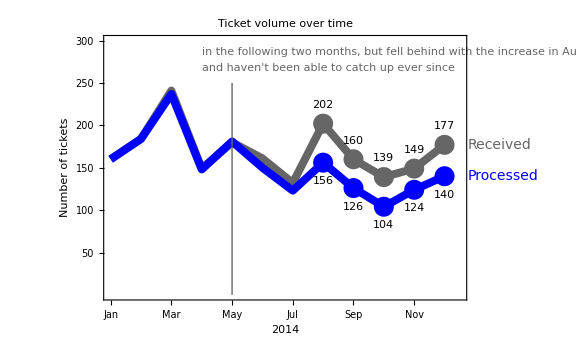

```mathematica
ticketsRec = {160,184,241,149,180,161,132,202,160,139,149,177};
ticketsProc= {160,184,237,148,181,150,123,156,126,104,124,140};
ticketDates = {"Jan", "Feb", "Mar", "Apr", "May", "Jun", "Jul",
			   "Aug", "Sep", "Oct", "Nov", "Dec"};
ptsRec = Transpose[{Range[12], ticketsRec}];
ptsProc = Transpose[{Range[12], ticketsProc}];

ptsRecAfter = Select[ptsRec, #⟦1⟧ > 7&];
ptsProcAfter = Select[ptsProc, #⟦1⟧ > 7&];
labelsRec = Map[Style[Text[#⟦2⟧, #+{0,22}], 
                      FontColor->Gray, FontSize->13]&,
                ptsRecAfter];
labelsProc = Map[Style[Text[#⟦2⟧, #-{0,22}], 
                       FontColor->Blue, FontSize->13]&,
                 ptsProcAfter];

text = {Row[{Style["2 employees quit in May.",Bold]," We nearly kept up with incoming volume"}],
"in the following two months, but fell behind with the increase in Aug,",
"and haven't been able to catch up ever since"};

ListPlot[{ptsRec, ptsProc, ptsRecAfter, ptsProcAfter},
	Joined->{True, True, False, False},
	PlotStyle->{
        Directive[GrayLevel[0.4],Thickness[0.01]],
        Directive[Blue,Thickness[0.01]],
        Directive[GrayLevel[0.4],PointSize[0.025]],
        Directive[Blue,PointSize[0.025]]
    },	
	PlotLabel->"Ticket volume over time",
	PlotLabels->Placed[{None, None, 
	                    Style["Received", GrayLevel[0.4], FontSize->14], 
	                    Style["Processed", Blue, FontSize->14]},
	                  {None, None, After, After}],

	Frame->{True, True, False, False},
	FrameLabel->{"2014", "Number of tickets"},
	LabelStyle->{13,13},
	PlotRange->{{1,12.5}, {0,300}},
	FrameTicks->{Map[{#⟦1⟧,#⟦2⟧,0}&, Transpose[{Range[12],ticketDates}]],
	            Range[50,300,50]},
	FrameTicksStyle->{12, 12},
	ImageSize->Large,
	
	Epilog->{
		labelsRec, labelsProc,
		
		GrayLevel[0.4],
		 Line[{{5,0}, {5,250}}],
		 
		 Table[Style[Text[text⟦n+1⟧, {4,310-18n}, {-1,1}],  
		       FontSize->12], {n, 0, Length[text]-1}]
	}
]
```

The key line here is

Table[Style[Text[text⟦n+1⟧, {4,310-18n}, {-1,1}],  
		   FontSize→12], {n, 0, 2}]

The Table goes through all the lines of text, and displays them one by one, at positions starting at {4,310}, and decreasing the height by 18 for each line after that. But what is that third argument {-1,1} of Text?

The third argument of Text, if present, dictates how the displayed text will be drawn relative to the coordinate given by the second argument. {-1,1} means that the upper-left corner of the box containing the text will be placed at the coordinate given in the second argument of Text. A value of {1,-1}, for example, means that the lower-right corner will be placed at the coordinate, and so on.

This is illustrated below:

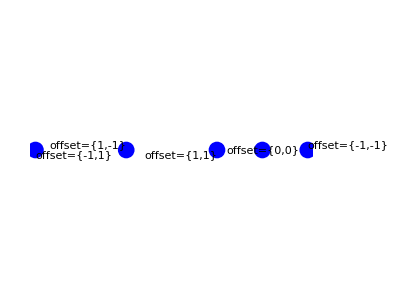

```mathematica
Graphics[{
	{Blue, PointSize[0.03],Point[{0,0}]}, Text[Framed["offset={-1,1}"], {0,0}, {-1,1}],
	{Blue, PointSize[0.03],Point[{1,0}]}, Text[Framed["offset={1,-1}"], {1,0}, {1,-1}],
	{Blue, PointSize[0.03],Point[{2,0}]}, Text[Framed["offset={1,1}"], {2,0}, {1,1}],
	{Blue, PointSize[0.03],Point[{3,0}]}, Text[Framed["offset={-1,-1}"], {3,0}, {-1,-1}],
	{Blue, PointSize[0.03],Point[{2.5,0}]}, Text[Framed["offset={0,0}"], {2.5,0}, {0,0}]
}]
```

### Placing the title

Although the block text we added looks good, it is clashing with the title. We would like to move the title up and to the left, so that it gets out of the way of the text. There is no good way of placing the text set by PlotLabel, so we use a trick here. We set PlotLabel to a blank line, and use the Epilog to place the title ourselves. The reason we still need to set PlotLabel to something, even though it is invisible, is that it creates space on the plot to allow for us to place the title. If we don’t set PlotLabel, the plot ends at the height of the vertical axis, and there is no room to display anything above it.

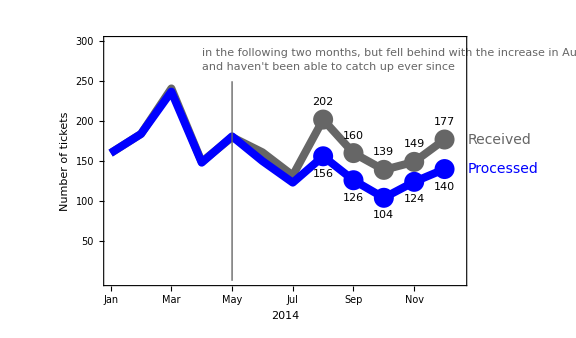

```mathematica
ticketsRec = {160,184,241,149,180,161,132,202,160,139,149,177};
ticketsProc= {160,184,237,148,181,150,123,156,126,104,124,140};
ticketDates = {"Jan", "Feb", "Mar", "Apr", "May", "Jun", "Jul",
			   "Aug", "Sep", "Oct", "Nov", "Dec"};
ptsRec = Transpose[{Range[12], ticketsRec}];
ptsProc = Transpose[{Range[12], ticketsProc}];

ptsRecAfter = Select[ptsRec, #⟦1⟧ > 7&];
ptsProcAfter = Select[ptsProc, #⟦1⟧ > 7&];
labelsRec = Map[Style[Text[#⟦2⟧, #+{0,22}], 
                      FontColor->Gray, FontSize->13]&,
                ptsRecAfter];
labelsProc = Map[Style[Text[#⟦2⟧, #-{0,22}], 
                       FontColor->Blue, FontSize->13]&,
                 ptsProcAfter];

text = {Row[{Style["2 employees quit in May.",Bold]," We nearly kept up with incoming volume"}],
"in the following two months, but fell behind with the increase in Aug,",
"and haven't been able to catch up ever since"};

ListPlot[{ptsRec, ptsProc, ptsRecAfter, ptsProcAfter},
	Joined->{True, True, False, False},
	PlotStyle->{
        Directive[GrayLevel[0.4],Thickness[0.01]],
        Directive[Blue,Thickness[0.01]],
        Directive[GrayLevel[0.4],PointSize[0.025]],
        Directive[Blue,PointSize[0.025]]
    },	
    PlotLabel->"\n",
	PlotLabels->Placed[{None, None, 
	                    Style["Received", GrayLevel[0.4], FontSize->14], 
	                    Style["Processed", Blue, FontSize->14]},
	                  {None, None, After, After}],

	Frame->{True, True, False, False},
	FrameLabel->{"2014", "Number of tickets"},
	LabelStyle->{13,13},
	PlotRange->{{1,12.5}, {0,300}},
	FrameTicks->{Map[{#⟦1⟧,#⟦2⟧,0}&, Transpose[{Range[12],ticketDates}]],
	            Range[50,300,50]},
	FrameTicksStyle->{12, 12},
	AspectRatio->1.0/1.7,
	ImageSize->Large,
	
	Epilog->{
		labelsRec, labelsProc,
		
		GrayLevel[0.4],
		 Line[{{5,0}, {5,250}}],
		 
		 Table[Style[Text[text⟦n+1⟧, {4,310-18n}, {-1,1}],  
		       FontSize->12], {n, 0, 2}],
		Style[Text["Ticket volume over time", {0,330}, {-1,-1}],
		            FontSize->20, GrayLevel[0.4]]		       
	}
]
```

This is the final version of the plot. As a final touch, we set the aspect ratio to make the plot look a little better.

### Challenge

Transform this plot...

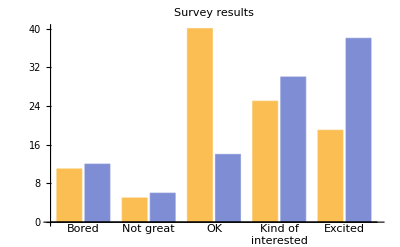

```mathematica
dataBefore = {11, 5, 40, 25, 19};
dataAfter = {12, 6, 14, 30, 38};
labels = {"Bored", "Not great", "OK", "Kind of\ninterested", "Excited"};
BarChart[Transpose[{dataBefore,dataAfter}],
	ChartLabels->{labels,None},
	PlotLabel->"Survey results",
	ChartLabels->{"before", "after"}
]
```

... into this:

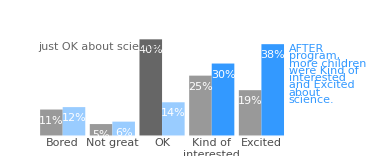

Hints:

The blue used here is RGBColor[0,0.5,1].

Define a function tint given by:

```mathematica
tint[colour:RGBColor[r_,g_,b_], intensity_] := Module[
	{colourVec = {r,g,b}},
	Apply[RGBColor, (1-colourVec)*(1-intensity) + colourVec]
]
```

This function turns an RGBColor into a faded version of the same colour; a low value of the parameter intensity will result in a more faded version of the colour passed in the first parameter. An intensity value of 1 leaves the colour the same:

```mathematica
lightBlue=RGBColor[0,0.5,1];
{lightBlue, tint[lightBlue,0.6], tint[lightBlue,0.3]}
```

{RGBColor[0, 0.5, 1],RGBColor[0.4, 0.7, 1.],RGBColor[0.7, 0.85, 1.]}

You will need to create space on the right side of the plot for the text in blue. One way to do so is to add dummy data with zero value (so there will be no bar) and a blank label.